# MLM and LSF Fitting

## Maximum Likelihood Method (MLM)

The maximum likelihood method determines a parameter  that maximizes (or respectively minimizes) a function of given measurements. This method revolves around the likelihood function, which can be formalized in one of two ways (depending on what the scenario calls for): 

 or 

To solve for the maximum/minimum , we simply use the first derivative test: .

```mathematica
L[f_,xi_]:=Product[f[x,λ],{x,xi}];
```

```mathematica
Param[L_]:=Solve[D[L, λ]==0,λ];
```

### Example

```mathematica
f[x_,λ_]:=1+λ x;
L[f,{1,2,3}]
Param[L[f,{1,2,3}]]
```

(1+λ) (1+2 λ) (1+3 λ)

{{λ→1/18 (-11-√13)},{λ→1/18 (-11+√13)}}

## Least Squares Fitting (LSF)

Least squares fitting is a method for finding a linear fit from a given set of data. This fit depends on summations of the x data, y data, x data squared, and x times y data. On top of that, if each measurement has a different uncertainty, then that can be taken into account as well. 

The form of the linear fit for the data is: , where:



If all the uncertainties, , are the same, then the forms for these simplify down to:

```mathematica
Δ[xi_,σi_]:=Sum[1/s^2,{s,σi}] Sum[x[[i]]^2/s[[i]]^2,{i,1,Length[s]}]-(Sum[x[[i]]/s[[i]]^2,{i,1,Length[s]}])^2;
α[xi_,yi_,σi_]:=1/Δ[xi,σi](Sum[y[[i]]/s[[i]]^2,{i,1,Length[s]}] Sum[x[[i]]^2/s[[i]]^2,{i,1,Length[s]}]-Sum[x[[i]] y[[i]]/s[[i]]^2,{i,1,Length[s]}]Sum[x[[i]]/s[[i]]^2,{i,1,Length[s]}]);
β[xi_,yi_,σi_]:=1/Δ[xi,σi](Sum[1/s^2,{s,σi}] Sum[x[[i]] y[[i]]/s[[i]]^2,{i,1,Length[s]}]-Sum[x[[i]]/s[[i]]^2,{i,1,Length[s]}]Sum[y[[i]]/s[[i]]^2,{i,1,Length[s]}]);
```

### Example

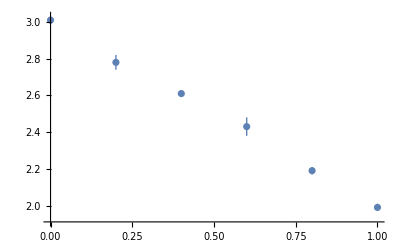

```mathematica
x={0,0.2,0.4,0.6,0.8,1};
y={3.01,2.78,2.61,2.43,2.19,1.99};
s={0.02,0.04,0.01,0.05,0.02,0.02};
ListPlot[Table[{x[[n]],Around[y[[n]],s[[n]]]},{n,1,6}]]
```

```mathematica
a=α[x,y,s]
```

3.0146

```mathematica
b=β[x,y,s]
```

-1.0221

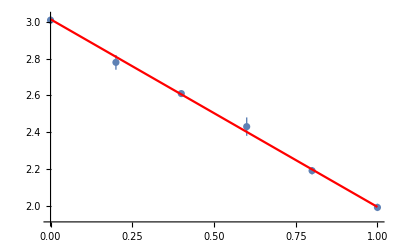

```mathematica
f[x_]:=a+b x;
p1=ListPlot[Table[{x[[n]],Around[y[[n]],s[[n]]]},{n,1,6}]];
p2=Plot[f[x],{x,0,1},PlotStyle->Red];
Show[p1,p2]
```